Michael T. McDonnell
M1
Math 3214, Calculus of Severable Variables
SSI 2014
2014/05/30

## Problem 1

```mathematica
d[n_]=2∫_(1/4)^(3/4) x^2*Sin[n π x]ⅆx
```

## Problem 2

```mathematica
f[x_,N_]:=∑_(n=1)^N d[n]*Sin[n*π*x]
```

## Problem 3

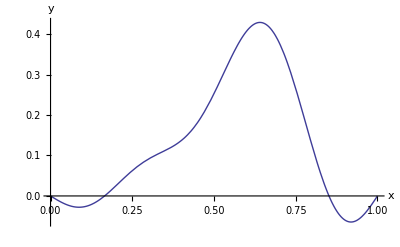

```mathematica
Plot[Tooltip[f[x, 5]], {x, 0, 1}, AxesLabel->{x,y}]
```

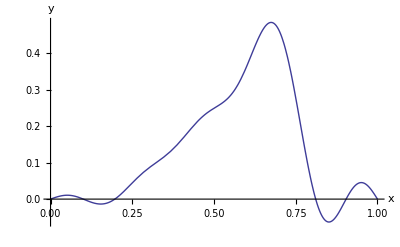

```mathematica
Plot[Tooltip[f[x,10]], {x,0,1}, AxesLabel->{"x","y"}]
```

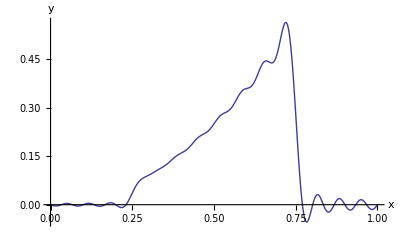

```mathematica
Plot[Tooltip[f[x,30]], {x,0,1}, AxesLabel->{"x","y"}]
```

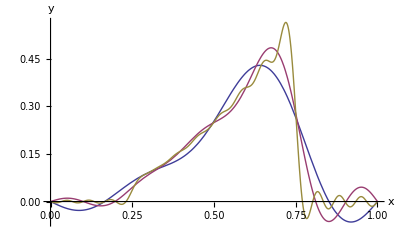

```mathematica
Plot[Tooltip[{f[x,5],f[x,10],f[x,30]}], {x,0,1}, AxesLabel->{"x","y"}]
```

## Problem 4

```mathematica
u [x_,t_]= ∑_(n=1)^30 d[n]*Cos[n π t]*Sin[n π x]
```

## Problem 5

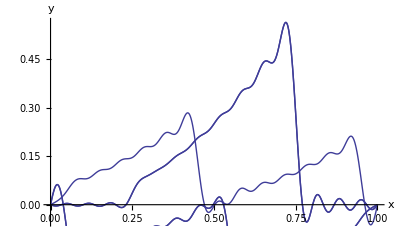

```mathematica
plot1 = Plot[Tooltip[u[x,0]], {x,0,1}];
plot2 = Plot[Tooltip[u[x,0.7]], {x,0,1}];
plot3 = Plot[Tooltip[u[x,1.3]],{x,0,1}];
plot4 = Plot[Tooltip[u[x,1.7]], {x,0,1}];
plot5 = Plot[Tooltip[u[x, 2]], {x,0,1}];

Show[plot1,plot2,plot3,plot4,plot5,AxesLabel-> {"x","y"}]
```

## Problem 6

```mathematica
Plot3D[u[x,t], {x,0,1}, {t,0,4}, AxesLabel ->  {x,y,z}]
```

-Graphics3D-